```mathematica
y[x_]:=2/(1-c Exp[x])
```

```mathematica
y[x]
```

2/(1-c ⅇ^x)

```mathematica
y[0]
```

2/(1-c)

```mathematica
y[x]/.c->0
```

2

```mathematica
y[x]/.c->1
```

2/(1-ⅇ^x)

```mathematica
y[x]/.c->-1
```

2/(1+ⅇ^x)

```mathematica
y[x]/.c->2
```

2/(1-2 ⅇ^x)

```mathematica
y[x]/.c->-2
```

2/(1+2 ⅇ^x)

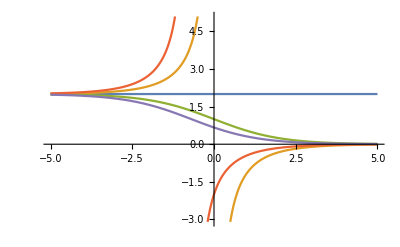

```mathematica
Plot[{2,2/(1-ⅇ^x),2/(1+ⅇ^x),2/(1-2 ⅇ^x),2/(1+2 ⅇ^x)},{x,-5,5}]
```